{{x→InterpolatingFunction[{{0.,30.}},<>],y→InterpolatingFunction[{{0.,30.}},<>]}}

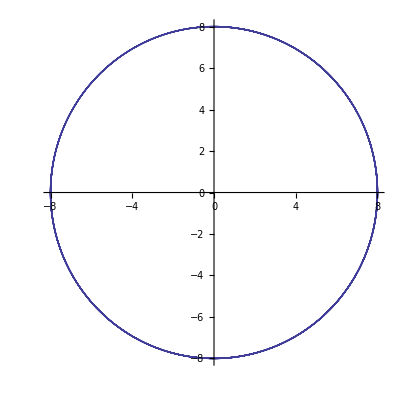

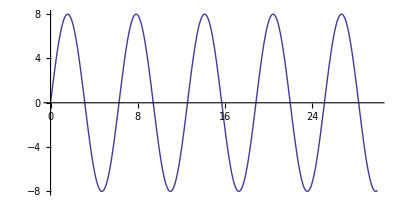

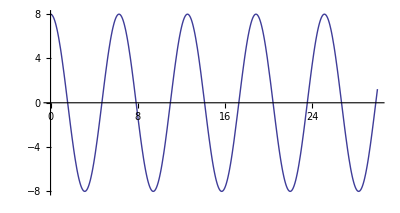

```mathematica
solve = NDSolve[
{x'[t]==y[t],y'[t] == -x[t], x[0] ==0, y[0] == 8},{x,y},{t,0,30}]
ParametricPlot[Evaluate[{x[t],y[t]}/.solve],{t,0,30}]
ParametricPlot[Evaluate[{t,x[t]       }/.solve],{t,0,30}]
ParametricPlot[Evaluate[{t,y[t]       }/.solve],{t,0,30}]
```